```mathematica
ClearAll;

Off[NonlinearModelFit::cvmit,NIntegrate::ncvb,FindFit::cvmit,NonlinearModelFit::sszero,LinearAlgebra`BLAS`TRSV::oflow,FindFit::nrlnum,FindFit::fdssnv,Part::partd,ReplaceAll::reps,NMaximize::nnum,ClebschGordan::phy]
```

Definition of Gauß, Lorentz, and Lorentz-transformed Lorentz functions

ILUM = (∫^∞)_e_th de 1/((σ_r-e)^2+σ_i^2)·1/((a_n-e)^2+b_n^2)

```mathematica
hat[l_]:=Sqrt[2 l+1];
HC=197.32858;

j0=0.5;
jlit={0.5,1.5};
MUL=1;
pi="-";

v18uixpath="/home/kirscher/kette_repo/ComptonLIT/v18uix_helium3/";

ILanaPlus[sr_,si_,a_,b_,eth_,c_]:=c^2/(((sr-a)^2+(si-b)^2) ((sr-a)^2+(si+b)^2)) (((sr-a)^2+b^2-si^2)/si (Pi/2+ArcTan[(sr-eth)/si])+((sr-a)^2-b^2+si^2)/b (Pi/2+ArcTan[(a-eth)/b])+(sr-a) Log[((sr-eth)^2+si^2)/((a-eth)^2+b^2)])
LorentzPlus[e_,a_,b_,eth_,c_]:=HeavisideTheta[e-eth] c^2/((a-e)^2+b^2);
```

import LIT data

i)    import data
       calculated with  <cpts_helion_v18uix_GAUSS_RGM.nb>

{0.5,1.5}

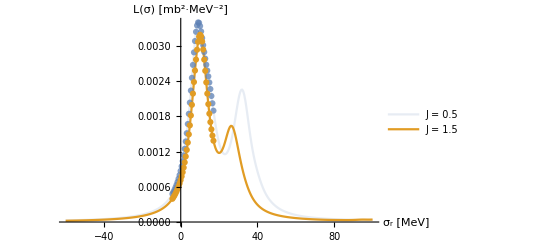

```mathematica
kR=ReadList[v18uixpath<>"kRange.dat",Real,RecordLists->True];
anzK=kR[[1]][[1]];k0=kR[[2]][[1]];dK=kR[[3]][[1]];
kR={};dataCrossLitfull={};dataCrossLit={};
For[photK=1,photK≤anzK,photK++,(
kR=AppendTo[kR,k0+photK dK];)]
Print[jlit];
kk=kR[[1]];

For[nJ=1,nJ≤Length[jlit],nJ++,(

dataCrossLitfull=AppendTo[dataCrossLitfull,N[ToExpression[Import[v18uixpath<>"real_LIT_J_"<>ToString[jlit[[nJ]]]<>"_k_"<>ToString[kk],"Table","FieldSeparators"->" ; "]]]];
dataCrossLit=AppendTo[dataCrossLit,N[ToExpression[Import[v18uixpath<>"real_LIT_J_"<>ToString[jlit[[nJ]]]<>"_k_"<>ToString[kk],"Table","FieldSeparators"->" ; "]]][[105;;145]]];
)];

nbrS=Length[dataCrossLit[[-1]]];
ub=dataCrossLit[[-1]][[-1]][[1]];
lb=dataCrossLit[[-1]][[1]][[1]];
sStellen=Range[lb,ub,(ub-lb)/nbrS];

emin=0.0;emax=20;
file=v18uixpath<>"E0.dat";

e0=Read[file];Close[file];
si=5;

labeljlit=("J = "<>ToString[#])&/@jlit;
Show[
ListLinePlot[dataCrossLitfull,PlotStyle->{Opacity[0.15],Large},AxesLabel->{"σ_r [MeV]","L(σ) [mb^2·MeV^-2]"},PlotLegends->labeljlit,PlotRange->Full],
ListPlot[dataCrossLit,PlotStyle->{Opacity[0.75],Small}]
]
```

Adapt the inspired (see above) and a randomly chosen Lorentz-transformed Lorentz basis to the model LIT and compare the thereby reconstructed cross section with the original data

Fit_max (J=0.5) = {0.00340307,{e→9.11732}}  peakth=0.0000430332

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Fit_max (J=1.5) = {0.00320274,{e→9.98543}}  peakth=0.000040387

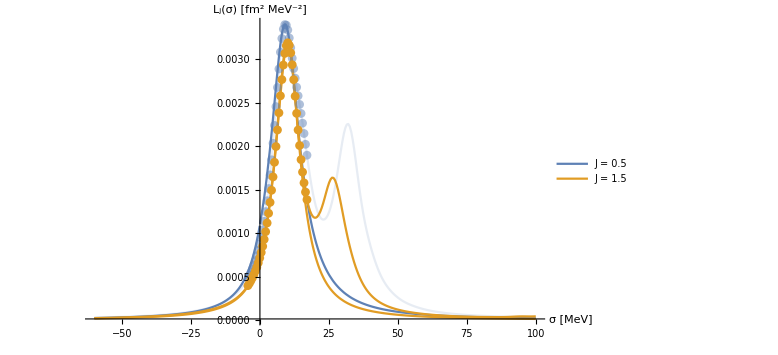
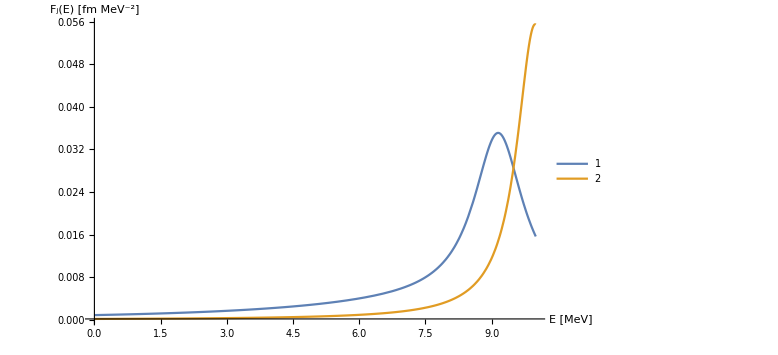
-Graphics- | -Graphics-

```mathematica
si=5;smin=-60;smax=100;

randdim=18;
anzF=1;

litfitLists={};lorentzbasplusLists={};
plotlistRESPONSEs={};plotlistLITs={};

For[nJ=1,nJ≤Length[jlit],nJ++,(

litfitList={};lorentzbasplusList={};

Monitor[i=0;
While[Length[litfitList]<anzF,

peakmatch=False;

While[peakmatch==False,

lorentzbasplus=Table[{RandomReal[{-10,10}],RandomReal[{0.1,4.2}],0.0},{n,randdim}];


brutedimp=Length[lorentzbasplus];
Clear[abrute];coeffsb=Array[abrute,brutedimp];

LinearLorentzModelb=Sum[ILanaPlus[sigmaR,si,lorentzbasplus[[i]][[1]],lorentzbasplus[[i]][[2]],lorentzbasplus[[i]][[3]],coeffsb[[i]]],{i,brutedimp}];

modelLorentzABCpm=FindFit[dataCrossLit[[nJ]],LinearLorentzModelb,coeffsb,sigmaR,MaxIterations->2000,PrecisionGoal->12,AccuracyGoal->12,Method->Automatic];

optPOSsol=Map[Rule[#[[1]],If[Abs[#[[2]]]>10^-16,Abs[#[[2]]],0.0]]&,modelLorentzABCpm];

expan[x_]:=LinearLorentzModelb/.optPOSsol/.sigmaR->x;
modmax=Maximize[expan[eee],eee];

datamax=Sort[dataCrossLit[[nJ]],#1[[2]]>#2[[2]]&][[1]];
	     peakth=Abs[datamax[[2]]]/79.;
peakdiff=Abs[modmax[[1]]-datamax[[2]]];
	     locth=Abs[datamax[[1]]]/79.;
locdiff=Abs[modmax[[2]][[1]][[2]]-datamax[[1]]];

If[((peakdiff<peakth)&&(locdiff<locth)),{peakmatch=True;AppendTo[litfitList,optPOSsol];AppendTo[lorentzbasplusList,lorentzbasplus]},peakmatch=False];

];

Print["Fit_max (J="<>ToString[jlit[[nJ]]]<>") = "<>ToString[Maximize[expan[e],e],TraditionalForm]<>"  peakth="<>ToString[peakth,TraditionalForm]];

];i,i--];

AppendTo[litfitLists,litfitList];AppendTo[lorentzbasplusLists,lorentzbasplusList];

cycl=Table[Rule[n,{n+1}],{n,Length[litfitList]-1}];
plotlistRESPONSE=Table[(Sum[LorentzPlus[e,lorentzbasplusList[[n]][[m]][[1]],lorentzbasplusList[[n]][[m]][[2]],lorentzbasplusList[[n]][[m]][[3]],coeffsb[[m]]],{m,brutedimp}])/.litfitList[[n]],{n,Length[litfitList]}];
plotlistLIT=Table[Sum[ILanaPlus[sigmaR,si,lorentzbasplusList[[n]][[i]][[1]],lorentzbasplusList[[n]][[i]][[2]],lorentzbasplusList[[n]][[i]][[3]],coeffsb[[i]]],{i,brutedimp}]/.litfitList[[n]]/.sigmaR->x,{n,Length[litfitList]}];

plotlistLITs=AppendTo[plotlistLITs,plotlistLIT];plotlistRESPONSEs=AppendTo[plotlistRESPONSEs,plotlistRESPONSE];

)];

Grid[{{
Show[
Plot[plotlistLITs,{x,smin,smax},PlotLegends->labeljlit,PlotRange->Full,PlotPoints->40,ImageSize->Large(*,Filling->cycl*),AxesLabel->{"σ [MeV]","L_j(σ) [fm^2 MeV^-2]"}],
ListLinePlot[dataCrossLitfull,PlotStyle->{Opacity[0.15],Large},PlotRange->Full],
ListPlot[dataCrossLit,PlotStyle->{Opacity[0.5],Medium}]
],
Plot[plotlistRESPONSEs,{e,0,10},PlotRange->Full,PlotLegends->Automatic(*,Filling->cycl*),AxesLabel->{"E [MeV]","F_j(E) [fm MeV^-2]"},
ImageSize->Large]}}]
```

strength functions from partial strength functions

F_((ν'L'νL)J)^(I_f I_i)(k,k;E)=(E-E_0)^2∑_I_n {L
I_fL'
I_iJ
I_n} F_ν'L'νL^(I_f I_i;I_n)(k,k;E)
i)   I_n is the total angular momentum of one element of the spectral representation of the intermediate Green function
i’) J  classifies the total angular-momentum transfer to the nucleus and assumes values  |L-L’|≤J≤|L+L’| for certain in- and out-going multi-polarities
ii) the energy-dependent prefactor is Siegert-form specific and does not appear in general!

```mathematica
λi=1;λf=1; (* in/outgoing-photon polarization = ±1 ? *)
Ll=1;
Llp=1;
Ji=Jf=0.5;Mi=Ji;Mf=Mi;
Jj={0,1};
labelj=("J = "<>ToString[#])&/@Jj;

kmin=5;kmax=20;kres=0.1;

strengthfunctionListpart=Table[Table[Table[((ee-e0)^2 plotlistRESPONSEs[[nJ]][[n]]/.e->ee)/.ee->(e0+kmag),{kmag,kmin,kmax,kres}],{n,1,anzF}],{nJ,1,Length[jlit]}];
strengthfunctionList=Table[Table[Total[Table[SixJSymbol[{Ll,Llp,Jj[[nJ]]},{Jf,Ji,jlit[[nJlit]]}] strengthfunctionListpart[[nJlit,nF,All]],{nJlit,Length[jlit]}]],{nJ,Length[Jj]}],{nF,anzF}];
```

real and imaginary parts of the (generalized) polarizabilities from strength functions

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_imag=2 π^2 (-)^(L+I_f+I_i)L̂ L̂' [F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i+k)+(-)^(L+L'+J)F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i-k')]
The second term does not contribute because the initial state is the ground- and not an excited state!

ECCE: the L̂’s come from the multipole expansion of the plane wave as do the 2π’s
ImPList [I_(n=1),I_(n=2),...] [fit_1,fit_2,...] [k_0... k_max]

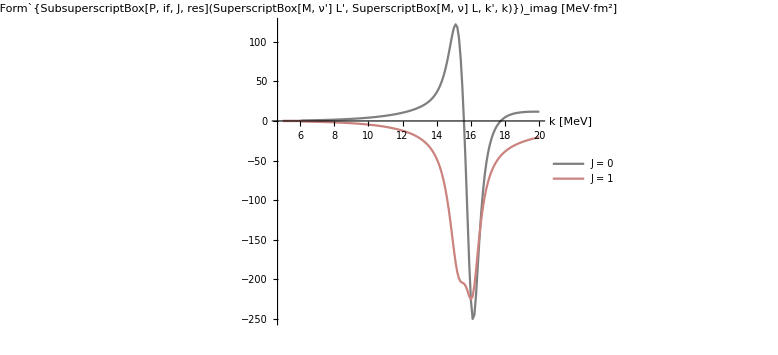

```mathematica
ImPList=Re[2 Pi^2 (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp] strengthfunctionList];
z=List[];
For[nJ=1,nJ≤Length[Jj],nJ++,(
atmp=ListLinePlot[ImPList[[All,nJ,All]],PlotRange->Full,AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_imag [MeV·fm^2]"},ImageSize->Large,Joined->True,DataRange->{kmin,kmax},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];Show[z]
```

imaginary part of the amplitude and total photodisintegration cross-section

{T_(L_f λ_f;L_i λ_i)^(I_f M_f;I_i M_i)(k⃗',k⃗)}_imag=(-)^(1+λ_f+I_f-M_i) ∑_(M_L_f M_L_i J) (-)^(L_i+L_f) (L̂)^2(I_f | J | I_i
-M_f | m | M_i) (L_i | L_f | J
M_i | M_f | -m) {P_(if,J)^(L_f λ_f,L_i λ_i)(k',k)}_imag D_(M_f,-λ_f)^L_f(0,θ,0) 

ECCE: 
i)   the polarization λ affects magnetic multipole ME’s, only (see eqs. (27,29,41) )
ii)  k⃗||(e⃗)_z ⇒ D_(M,λ)^L(R)=1
iii)

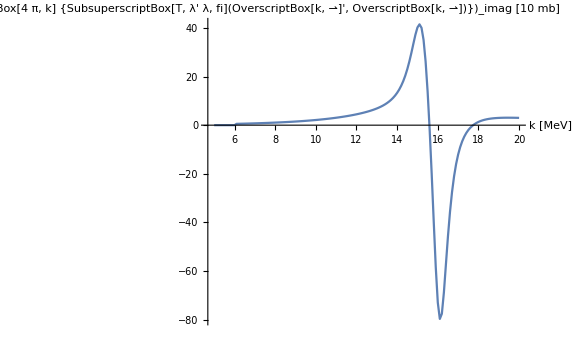

```mathematica
ImT[Mf_,Mi_,λf_,λi_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Jj],nJ++,(
compo=hat[Jj[[nJ]]]^2 ImPList[[All,nJ,All]];
For[Mm=-Ll,Mm≤Ll,Mm++,(
For[Mmp=-Llp,Mmp≤Llp,Mmp++,
(
ampli+=ThreeJSymbol[{Jf,-Mf},{Jj[[nJ]],Mf-Mi},{Ji,Mi}] ThreeJSymbol[{Ll,Mm},{Llp,Mmp},{Jj[[nJ]],-Mm-Mmp}] WignerD[{Llp,Mmp,-λf},0,θ,0] compo;
)];)];)];
Return[(-1)^(1+λf+Jf-Mi)*ampli]
]
DissCross[Mf_,Mi_,λf_,λi_,θ_]:=Table[(4 Pi/Table[kmag,{kmag,kmin,kmax,kres}]) fit,{fit,ImT[Mf,Mi,λf,λi,θ]}];
ListLinePlot[Re[DissCross[Jf,Ji,1,1,0]],PlotRange->{Full,Full},AxesLabel->{"k [MeV]","(TraditionalForm`FractionBox[4  π, k] {SubsuperscriptBox[T, λ' λ, fi](OverscriptBox[k, ⇀]', OverscriptBox[k, ⇀])})_imag [10 mb]"}(*,Filling->cycl*),ImageSize->Large,Joined->True,DataRange->{kmin,kmax}]
```

{P_(if,J)^res(M^ν' L',M^ν L,k',k)}_real=2π (-)^(L+I_f+I_i)L̂ L̂'  𝓅∫_E_0^∞ dE[(F_((ν'L'νL)J)^(I_f I_i)(k,k;E))/(E-E_i-k)+(-)^(L+L'+J)(F_((ν'L'νL)J)^(I_f I_i)(k,k;E))/(E-E_i+k')]

```mathematica
prefak=2 Pi (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp];
RePEoneJkernelAList=Table[ strengthfunctionList[[n]]/(ee-(e0+kkk)),{n,anzF}];
RePEoneJkernelBList=Table[(-1)^(Ll+Llp+Jj) strengthfunctionList[[n]]/(ee-(e0-kkk)),{n,anzF}];

gPAList=NIntegrate[RePEoneJkernelAList,{ee,e0,e0+kkk,Infinity},Method->"PrincipalValue"];
gPBList=NIntegrate[RePEoneJkernelBList,{ee,e0,e0-kkk,Infinity},Method->"PrincipalValue"];
genPolList=prefak (NIntegrate[RePEoneJkernelAList,{ee,e0,e0+kkk,Infinity},Method->"PrincipalValue"]+NIntegrate[RePEoneJkernelBList,{ee,e0,e0-kkk,Infinity},Method->"PrincipalValue"]);
(*
Plot[{RePEoneJkernelAList/.kkk->1,RePEoneJkernelBList/.kkk->1},{ee,emin,emax},PlotRange->Full,PlotLegends->{"F_((ν'L'νL)J)^I_f","(-)"},AxesLabel->{"E [MeV]",""},PlotStyle->{{Red,Dashed},{Blue,Dashed}},PlotLabel->"k="<>ToString[kkk]<>" MeV",ImageSize->Large]*)
```

$Aborted

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

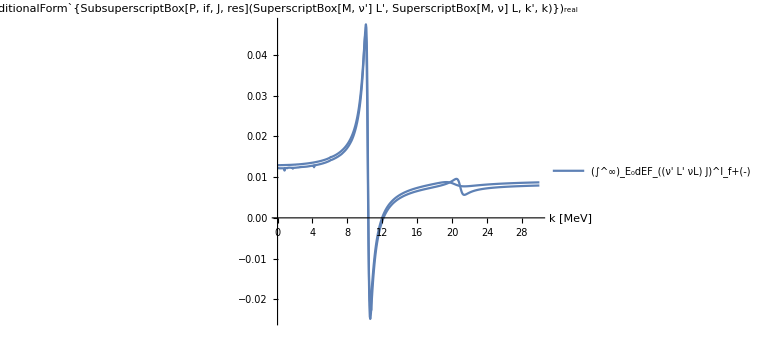

```mathematica
Plot[genPolList,{kkk,kmin,kmax},PlotRange->Full,PlotLegends->{"(∫^∞)_E_0dEF_((ν' L' νL) J)^I_f+(-)"},AxesLabel->{"k [MeV]","(TraditionalForm`{SubsuperscriptBox[P, if, J, res](SuperscriptBox[M, ν'] L', SuperscriptBox[M, ν] L, k', k)})_real"},PlotPoints->10,ImageSize->Large]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

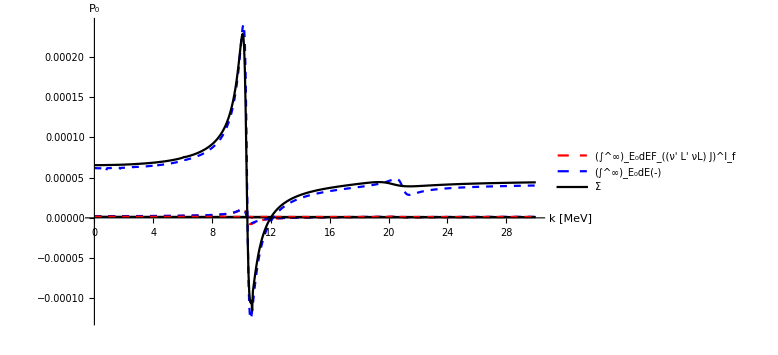

```mathematica
Plot[{gPAList,gPBList,genPolList},{kkk,kmin,kmax},PlotRange->Full,PlotLegends->{"(∫^∞)_E_0dEF_((ν' L' νL) J)^I_f","(∫^∞)_E_0dE(-)","Σ"},AxesLabel->{"k [MeV]","P_0"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}},PlotPoints->10,ImageSize->Large]
```